## 程序：

```mathematica
(*初始化程序*)
b=20;(*右区间b*)
division=1000;(*单位区间细分度*)
tol=0.0001;(*允许两者的误差精度*)
result={};(*存储结果*)

If[Floor[division*(b-1)]==division*(b-1),,Print["请为division取一个能够使division*(b-1)为正整数的数值"];Throw[$Failed];](*验证初始数据*)
testdata=Table[1+1/division*i,{i,0,division*(b-1)}];(*生成测试集*)
(*题目条件f(x),F的定义*)
f[x_]:=Piecewise[{{x-1,1≤x<1+(b-1)/3},
{-2(x-(1+b)/2),1+(b-1)/3≤x<(1+b)/2},
{2(x-(1+b)/2),(1+b)/2≤x<1+2*(b-1)/3},
{b-x,1+2*(b-1)/3≤x≤b}}];

F={1,2,3,Abs[2-b],Abs[-1+b],Abs[b],2 Abs[b],3Abs[b],Abs[1+b],Abs[2+b],Abs[-1+2b],Abs[1+2b],Abs[2-x],Abs[1-b-x],Abs[b-x],Abs[1+b-x],Abs[2b-x],Abs[-1+x],Abs[x],2Abs[x],3Abs[x],Abs[1+x],Abs[2+x],Abs[1-b+x],Abs[b+x],Abs[1+b+x],Abs[2b+x],Abs[-1+2x],Abs[1+2x],Abs[-b+2x],Abs[b+2x]};
F1=Complement[F,{1}];
F2=Complement[F,{Abs[x]}];
F3=Complement[F,{Abs[b]}];
(*g的定义*)
g=Min[Abs[F1-1],Abs[F2-x],Abs[F3-b]];

(*主程序*)
time=Timing[
(*初始化变量*)
start=0;
end=0;
flag=0;
status=0;

(*核心程序*)
For[j=1,j≤Length[testdata],j++,
point=testdata[[j]];
(*进入恒等区间，记录起点*)
If[Abs[(g/.x->point)-f[point]]≤tol && flag==0,start=testdata[[j]];flag=1;status=1;,
(*超过容差时，取前一位作为区间终点*)
If[Abs[(g/.x->point)-f[point]]>tol  && flag==1,end=testdata[[j-1]];flag=0;,
(*状态码突变，记录起点和终点*)
If[status==1 && flag==0,AppendTo[result,{start,end}];status=0;];
];
];
];
(*结尾特判*)
If[status==1 && flag==1,AppendTo[result,{start,b}];status=0;]; 
];
Print["Finished in ",time[[1]]," seconds"];
```

Finished in 2.9375 seconds

## 实验结果：

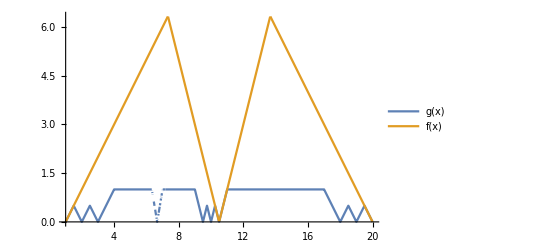

函数图像如上

区间：[1 , 3/2] 是f(x)与g(x)的一个恒等区间

区间：[41/4 , 11] 是f(x)与g(x)的一个恒等区间

区间：[39/2 , 20] 是f(x)与g(x)的一个恒等区间

结果保存在变量 resultsection 中

(1 | 3/2
41/4 | 11
39/2 | 20)

```mathematica
MatrixForm[result];(*显示所有的result，包含所有交点，这里隐藏了，我们想要的是区间*)
Plot[{g,f[x]},{x,1,b},PlotLegends->{"g(x)","f(x)"}](*显示所有图像*)
Print["函数图像如上\n"];
resultsection={};(*储存区间结果*)

(*删除所有的点区间*)
For[i=1,i≤Length[result],i++,
If[result[[i,1]]≠ result[[i,2]],(*区间长度不为零就记录下来*)
AppendTo[resultsection,result[[i]]];
Print["区间：[",result[[i,1]]," , ", result[[i,2]],"] 是f(x)与g(x)的一个恒等区间"];
];
];
Print["结果保存在变量 resultsection 中"];
MatrixForm[resultsection]
```